```mathematica
(* Microlensing setup described by Oguri 2017 *)
β1[θ1_,θ2_]:= θ1/μr - θ1/(θ1^2 + θ2^2)
β2[θ1_,θ2_] := θ2/μt-θ2/(θ1^2+θ2^2)
```

```mathematica
β:={β1[θ1,θ2],β2[θ1,θ2]}
```

```mathematica
θ :={θ1, θ2}
```

```mathematica
InvMagnefication = FullSimplify[Table[Table[D[β[[i]],θ[[j]]],{j,1,2}],{i,1,2}]]
```

{{((θ1-θ2) (θ1+θ2))/((θ1^2+θ2^2)^2)+1/μr,(2 θ1 θ2)/((θ1^2+θ2^2)^2)},{(2 θ1 θ2)/((θ1^2+θ2^2)^2),(-θ1^2+θ2^2)/((θ1^2+θ2^2)^2)+1/μt}}

```mathematica
InvMagnefication=FullSimplify[InvMagnefication/.θ1->r*Cos[ϕ]/.θ2->r*Sin[ϕ],Assumptions->Element[ϕ,Reals]]
```

{{1/μr+Cos[2 ϕ]/r^2,Sin[2 ϕ]/r^2},{Sin[2 ϕ]/r^2,1/μt-Cos[2 ϕ]/r^2}}

```mathematica
Simplify[Det[InvMagnefication],Assumptions->r>0&&μt>0&&μr>0]
```

(r^4-μr μt+r^2 (μr-μt) Cos[2 ϕ])/(r^4 μr μt)

```mathematica
CriticalCurves=Solve[(r^4-μr μt+r^2 (μr-μt) Cos[2 ϕ])/(r^4 μr μt)==0 ,{r}]
```

{{r→-1/(√2)(√(-μr Cos[2 ϕ]+μt Cos[2 ϕ]-√(4 μr μt+(μr Cos[2 ϕ]-μt Cos[2 ϕ])^2)))},{r→1/(√2)(√(-μr Cos[2 ϕ]+μt Cos[2 ϕ]-√(4 μr μt+(μr Cos[2 ϕ]-μt Cos[2 ϕ])^2)))},{r→-1/(√2)(√(-μr Cos[2 ϕ]+μt Cos[2 ϕ]+√(4 μr μt+(μr Cos[2 ϕ]-μt Cos[2 ϕ])^2)))},{r→1/(√2)(√(-μr Cos[2 ϕ]+μt Cos[2 ϕ]+√(4 μr μt+(μr Cos[2 ϕ]-μt Cos[2 ϕ])^2)))}}

```mathematica
(* Plotting the critical curves using polar plots*)
(* Reference: https://reference.wolfram.com/language/ref/PolarPlot.html *)
```

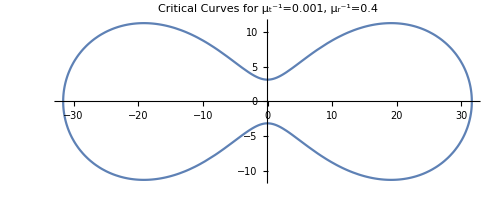

```mathematica
Show[
PolarPlot[r/.(CriticalCurves[[1]]/.μt->0.001^(-1)/.μr->0.1^(-1)),{ϕ,0,2*π}],
PolarPlot[r/.(CriticalCurves[[3]]/.μt->0.001^(-1)/.μr->0.1^(-1)),{ϕ,0,2*π}],
PlotRange->All,PlotLabel->"Critical Curves for μ_t^-1=0.001, μ_r^-1=0.4"]
```

```mathematica
(* Plotting the caustics *)
```

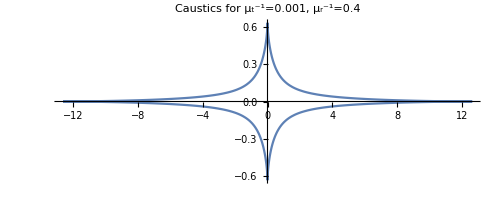

```mathematica
Show[
ParametricPlot[{β1[r*Cos[ϕ],r*Sin[ϕ]],β2[r*Cos[ϕ],r*Sin[ϕ]]}/.CriticalCurves[[1]]/.μt->0.001^(-1)/.μr->0.4^(-1),{ϕ,0,2π}],
ParametricPlot[{β1[r*Cos[ϕ],r*Sin[ϕ]],β2[r*Cos[ϕ],r*Sin[ϕ]]}/.CriticalCurves[[3]]/.μt->0.001^(-1)/.μr->0.4^(-1),{ϕ,0,2π}],
PlotRange->All,PlotLabel->"Caustics for μ_t^-1=0.001, μ_r^-1=0.4"
]
```

```mathematica
(* Discussion of critical curve solutions *)
```

```mathematica
(* Suppose Subscript[μ, r]>0, then for ϕ=0*)
(* if Subscript[μ, t] > 0, we always have r=Sqrt[Subscript[μ, t]]*)
(* if Subscript[μ, t] < 0, we don't have solution and the lobe is vertical*)
```

```mathematica
(* Suppose Subscript[μ, r] > 0 then for ϕ=π/2 *)
(* if Subscript[μ, t] > 0, we have r=Sqrt[Subscript[μ, r]] only, indicating the narrowest neck of the lobe*)
(* if Subscript[μ, t] < 0,we have r= Sqrt[Subscript[μ, r]] and r = Sqrt[Subscript[μ, t]] for the top and bottom of the lobe*)
```

```mathematica
(* Caustic crossing time *)
(* The caustic crossing time is the time needed to cross the caustics *)
```

```mathematica
Msun = 1477; (*m*)
kpc = 3.086*10^(19); (* m *)
Gpc  =3.086*10^(25) ;(* m *)
yr = 3.155692511163×10^7; (*s*)
```

```mathematica
Clear[u,Dls,Dl,Ds,βw,μt,v,tE]
```

```mathematica
θE=Sqrt[4*M*Dls/(Ds*Dl)];
βw =θE/Sqrt[μt] ;(* Caustic width along the y-axis*)
u =v/Ds;(*Approximated as the velocity of the cluster because of high μt*)
tE=βw/u ;(* Einstein crossing time *)
```

```mathematica
(tE/.M->Msun*M/.Dls->Dls*Gpc/.Ds->Ds*Gpc/.Dl->Dl*Gpc/.μt->100μt/.v->500*10^3*v)/yr
```

(2.70616 Ds √((Dls M)/(Dl Ds)))/(v √μt)

```mathematica
(* Lens plane mapping as source move across critical curves *)
```

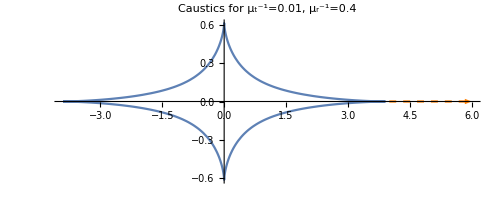

```mathematica
Block[{μt=0.01^(-1),μr=0.4^(-1),βmin=4,βmax=6},Show[
ParametricPlot[{β1[r*Cos[ϕ],r*Sin[ϕ]],β2[r*Cos[ϕ],r*Sin[ϕ]]}/.CriticalCurves[[1]],{ϕ,0,2π}],
ParametricPlot[{β1[r*Cos[ϕ],r*Sin[ϕ]],β2[r*Cos[ϕ],r*Sin[ϕ]]}/.CriticalCurves[[3]],{ϕ,0,2π}],
ParametricPlot[{t,0},{t,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x],
PlotRange->All,PlotLabel->StringForm["Caustics for μ_t^-1=``, μ_r^-1=``",μt^(-1),μr^(-1)]
]]
```

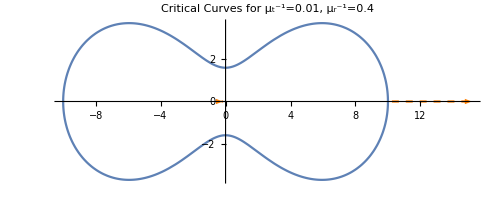

```mathematica
Block[{μt=0.01^(-1),μr=0.4^(-1),βmin=4,βmax=6},Show[
PolarPlot[r/.(CriticalCurves[[1]]),{ϕ,0,2*π}],
PolarPlot[r/.(CriticalCurves[[3]]),{ϕ,0,2*π}],
ParametricPlot[{1/2 (β* μr-√μr √(4+β^2* μr)),0},{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x], (*Case 1: θ2 = 0*)
ParametricPlot[{1/2 (β* μr+√μr √(4+β^2* μr)),0},{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x], 
(* Case 2: θ2 != 0*) 
ParametricPlot[{θ11,Sqrt[μt-θ11^2]}/.θ11->β*(1/μr-1/μt)^(-1),{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x],
ParametricPlot[{θ11,-Sqrt[μt-θ11^2]}/.θ11->β*(1/μr-1/μt)^(-1),{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x],
PlotRange->All,PlotLabel->StringForm["Critical Curves for μ_t^-1=``, μ_r^-1=``",μt^(-1),μr^(-1)]]
]
```

```mathematica
(* Remark: Originally I tried to see if I can do the mapping along the y-axis, but turns out I mixed up x-y axis and get a result for x-axis movements instead, but anyway.... *)
Clear[μt,μr]
```

```mathematica
Block[{},βx=Sqrt[μt](1/μr-1/μt)] (* Caustic size along x direction*)
```

(1/μr-1/μt) √μt

```mathematica
Block[{μt=0.01^(-1),μr=0.4^(-1)},βx=Sqrt[μt](1/μr-1/μt)]
```

3.9

```mathematica
(* Vertical crossing *)
```

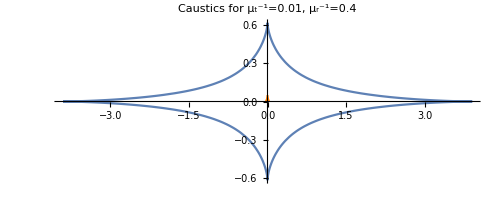

```mathematica
Block[{μt=0.01^(-1),μr=0.4^(-1),βmin=0,βmax=0.05},Show[
ParametricPlot[{β1[r*Cos[ϕ],r*Sin[ϕ]],β2[r*Cos[ϕ],r*Sin[ϕ]]}/.CriticalCurves[[1]],{ϕ,0,2π}],
ParametricPlot[{β1[r*Cos[ϕ],r*Sin[ϕ]],β2[r*Cos[ϕ],r*Sin[ϕ]]}/.CriticalCurves[[3]],{ϕ,0,2π}],
ParametricPlot[{0,t},{t,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x],
PlotRange->All,PlotLabel->StringForm["Caustics for μ_t^-1=``, μ_r^-1=``",μt^(-1),μr^(-1)]
]]
```

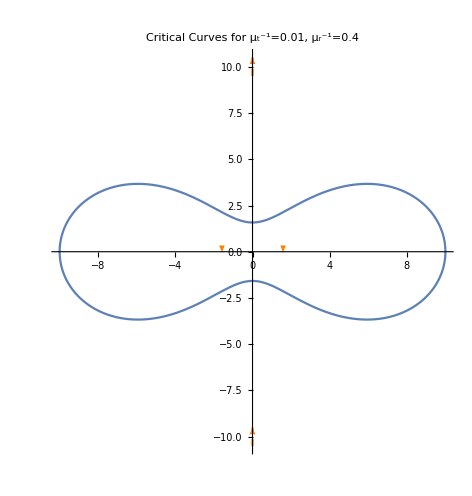

```mathematica
Block[{μt=0.01^(-1),μr=0.4^(-1),βmin=-0.01,βmax=0.01},Show[
PolarPlot[r/.(CriticalCurves[[1]]),{ϕ,0,2*π}],
PolarPlot[r/.(CriticalCurves[[3]]),{ϕ,0,2*π}],
ParametricPlot[{0,1/2 (β* μt-√μt √(4+β^2* μt))},{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x], (*Case 1: θ2 = 0*)
ParametricPlot[{0,1/2 (β* μt+√μt √(4+β^2* μt))},{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x], 
(* Case 2: θ2 != 0*) 
ParametricPlot[{Sqrt[μr-θ22^2],θ22}/.θ22->β*(1/μt-1/μr)^(-1),{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x],
ParametricPlot[{-Sqrt[μr-θ22^2],θ22}/.θ22->β*(1/μt-1/μr)^(-1),{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x],
PlotRange->All,PlotLabel->StringForm["Critical Curves for μ_t^-1=``, μ_r^-1=``",μt^(-1),μr^(-1)]]
]
```

```mathematica
Block[{},βx=Sqrt[μr](1/μr-1/μt)] (* Caustic size along x direction*)
```

√μr (1/μr-1/μt)

```mathematica
Block[{μt=0.01^(-1),μr=0.4^(-1)},βx=Sqrt[μr](1/μr-1/μt)]
```

0.616644

```mathematica
(* Plotting the time delay curves *)
```

```mathematica
(* Time in 4 Subscript[M, L] and angles in θE*)
(* Ingredients: *)
(* 
	Lens potential: ψ=(1/2)κ(θ1^2 +θ2^2)+(1/2)γ(θ1^2 - θ2^2) + θE^2 Log(Sqrt[θ1^2 + θ2^2 ])
This can be simplified by factoring out the Einstein radius: 

ψ= θE^2 [(1/2)κ((θ1/θE)^2 +(θ2/θE)^2)+(1/2)γ((θ1/θE)^2 - (θ2/θE)^2) + Log(Sqrt[(θ1/θE)^2 + (θ1/θE)^2 ])] + const 

Recall θE=Sqrt[4*M*Dls/(Ds*Dl)], and the actual timing potential t = T*[(1/2)(θ-β)^2 - ψ], where T* = (1+zl)Dl*Ds/Dls, but we can pull out θE^2 inside the bracket, this left us with:
T = (1+zl) 4Ml ((1/2)(θ/θE-β/θE)^2 - ψ/θE^2)
	Main point: The time scale is set by 4Ml
*)
```

```mathematica
ψd[θ1_,θ2_,β1_,β2_]:=(1/2)*((θ1-β1)^2 + (θ2-β2)^2) - Log[Sqrt[θ1^2 + θ2^2]]+(1/2)*κ*(θ1^2 + θ2^2)+(1/2)*γ*(θ1^2 -θ2^2)
```

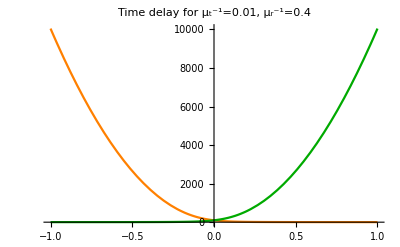

```mathematica
Block[{μt=0.01^(-1),μr=0.4^(-1),βmin=-1,βmax=1,κ=1-(μr^(-1)+μt^(-1))/2,γ=(μt^(-1)-μr^(-1))/2},Show[
Plot[ψd[0,1/2 (β* μt-√μt √(4+β^2* μt)),0,β],{β,βmin,βmax},PlotStyle->{Orange}],

Plot[ψd[0,1/2 (β* μt+√μt √(4+β^2* μt)),0,β],{β,βmin,βmax},PlotStyle->{Darker[Green]}],
(*ParametricPlot[{0,1/2 (β* μt-√μt √(4+β^2* μt))},{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x], (*Case 1: θ2 = 0*)
ParametricPlot[{0,1/2 (β* μt+√μt √(4+β^2* μt))},{β,βmin,βmax},PlotStyle->{Orange,Dashed}]/. Line[x__]:>Arrow[x], *)
(* Case 2: θ2 != 0*) 
PlotRange->Automatic,PlotLabel->StringForm["Time delay for μ_t^-1=``, μ_r^-1=``",μt^(-1),μr^(-1)]]
]
```

```mathematica
N[ψd[0,1/2 (a* μt-√μt √(4+a^2* μt)),0,a]/.κ->1-(μr^(-1)+μt^(-1))/2/.γ->(μt^(-1)-μr^(-1))/2/.μt->0.01^(-1)/.μr->0.4^(-1)/.a->0.0]
```

97.1974

```mathematica
(* Question: What about the other two images?*)
```